```mathematica
dist=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/2D/dist.txt","Table"];distConf=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/2D/distConf.txt","Table"];distMarg=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/2D/distMarg.txt","Table"];
```

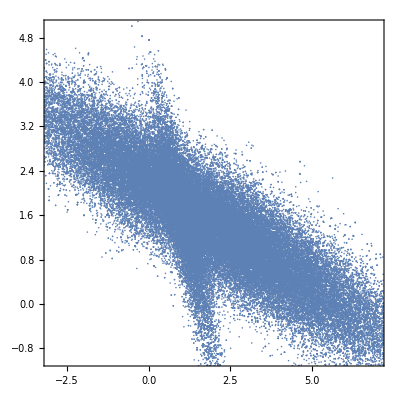

```mathematica
ListPlot[Table[{dist[[i,2]],dist[[i,3]]},{i,Length[dist]}],PlotRange->{{-3,7},{-1,5}},Frame->True,AspectRatio->1]
```

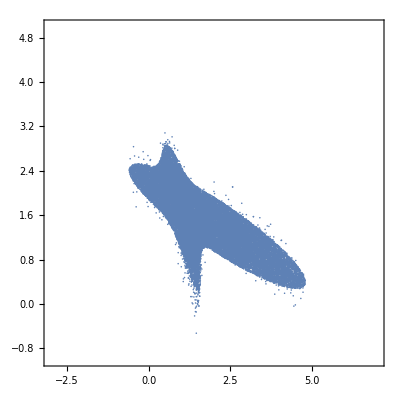

```mathematica
ListPlot[Table[{distConf[[i,2]],distConf[[i,3]]},{i,Length[distConf]}],PlotRange->{{-3,7},{-1,5}},Frame->True,AspectRatio->1]
```

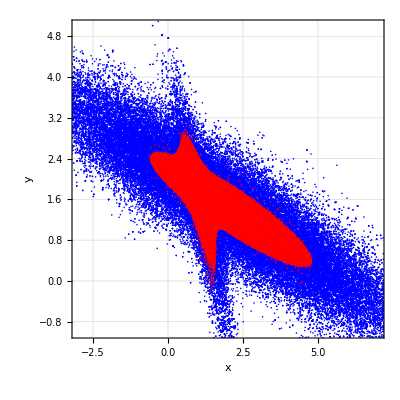

```mathematica
contour2D=ListPlot[{Table[{dist[[i,2]],dist[[i,3]]},{i,Length[dist]}],Table[{distConf[[i,2]],distConf[[i,3]]},{i,Length[distConf]}]},PlotRange->{{-3,7},{-1,5}},Frame->True,AspectRatio->1,PlotStyle->{Blue,Red},GridLines->Automatic,FrameLabel->{"x","y"}]
```

```mathematica
Export["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/2D/contour2D.pdf",contour2D(*/.{EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i}*)];
```

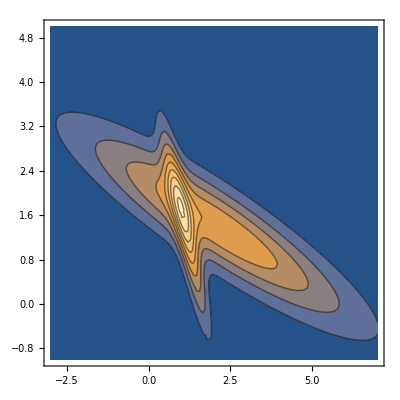

```mathematica
ContourPlot[Exp[-((x-1.1)^2/0.2/0.2+2*0.9*(x-1.1)*(y-1.4)/0.2/0.5+(y-1.4)^2/0.5/0.5)/2]+Exp[-((x-2.1)^2/1.2/1.2+2*0.9*(x-2.1)*(y-1.4)/1.2/0.5+(y-1.4)^2/0.5/0.5)/2],{x,-3,7},{y,-1,5},PlotRange->All]
```

```mathematica
Plot3D[Exp[-((x-1.1)^2/0.2/0.2+2*0.9*(x-1.1)*(y-1.4)/0.2/0.5+(y-1.4)^2/0.5/0.5)/2]+Exp[-((x-2.1)^2/1.2/1.2+2*0.9*(x-2.1)*(y-1.4)/1.2/0.5+(y-1.4)^2/0.5/0.5)/2],{x,-3,7},{y,-1,5},PlotRange->All]
```

-Graphics3D-

```mathematica
p[x_,y_]:=Exp[-((x-1.1)^2/0.2/0.2+2*0.9*(x-1.1)*(y-1.4)/0.2/0.5+(y-1.4)^2/0.5/0.5)/2]+Exp[-((x-2.1)^2/1.2/1.2+2*0.9*(x-2.1)*(y-1.4)/1.2/0.5+(y-1.4)^2/0.5/0.5)/2];
```

```mathematica
p[x_]:=NIntegrate[p[x,y],{y,-Infinity,Infinity}];
```

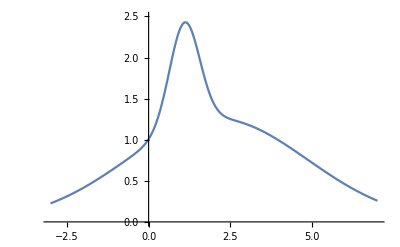

```mathematica
Plot[p[x],{x,-3,7},PlotRange->{{-3,7},{0,2.5}}]
```

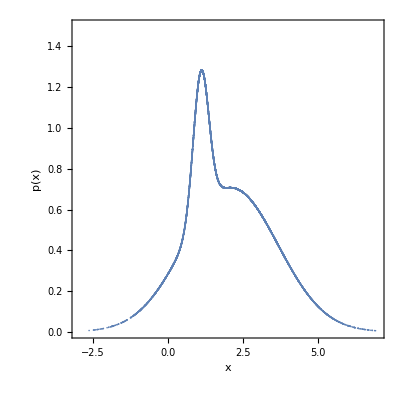

```mathematica
margin=ListPlot[Table[{distMarg[[i,2]],distMarg[[i,1]]},{i,Length[distMarg]}],PlotRange->{{-3,7},{0,1.5}},Frame->True,AspectRatio->1,FrameLabel->{"x","p(x)"}]
```

```mathematica
Export["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/2D/margin.pdf",margin(*/.{EdgeForm[],r_?(MemberQ[{RGBColor,Hue,CMYKColor,GrayLevel},Head[#]]&),i___}:>{EdgeForm[r],r,i}*)];
```